```mathematica
Clear["Global`*"]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"solutions_and_parameters","plotstyle.m"}]];
Get[FileNameJoin[{NotebookDirectory[],"solutions_and_parameters","colors.m"}]];
Get[FileNameJoin[{NotebookDirectory[],"solutions_and_parameters","model_parameters.m"}]];
Get[FileNameJoin[{NotebookDirectory[],"solutions_and_parameters","solutions.m"}]];
```

```mathematica
x0v=0.4*λv;
wv=0.4*λv;
wCompv=0.8*λv;
Lv=1.8* λv;
```

## Two morhogen growth rule + feedback

Growth stops in any case, because the growth threshold at the middle (for symmetrical case) is reached. If the final source region width w is not zero at the growth arrest, that the thresholds for growth and feedback are connected with final parameters as follows.

```mathematica
SolutionSteadyRight[x_, x0_,  λ_, α_, w_, β_, Diff_, L_] := 2 α /(β Sinh[L/λ])  Sinh[w/(2 λ)] Cosh[(w + 2 x0)/(2 λ)] Cosh[(L - x)/λ] ;
```

#### Θgr = SolutionSteadyRight[Lfinal/2, x0final, λ, α, wComp - x0final, β, Diff, Lfinal]

```mathematica
SolutionSteadyRight[Lfinal/2, x0final,  λ, α, wComp - x0final, β, Diff, Lfinal]
```

(2 α Cosh[Lfinal/(2 λ)] Cosh[(wComp+x0final)/(2 λ)] Csch[Lfinal/λ] Sinh[(wComp-x0final)/(2 λ)])/β

#### Θfb = SolutionSteadyRight[Lfinal - x0final, x0final, λ, α, wComp - x0final, β, Diff, Lfinal]

```mathematica
SolutionSteadyRight[Lfinal - x0final, x0final,  λ, α, wComp - x0final, β, Diff, Lfinal]
```

(2 α Cosh[x0final/λ] Cosh[(wComp+x0final)/(2 λ)] Csch[Lfinal/λ] Sinh[(wComp-x0final)/(2 λ)])/β

```mathematica
Θgr[λ_,  α_, wComp_, β_, Diff_, Lfinal_, x0final_]:=(2 α Cosh[Lfinal/(2 λ)] Cosh[(wComp+x0final)/(2 λ)] Csch[Lfinal/λ] Sinh[(wComp-x0final)/(2 λ)])/β;
Θfb[λ_,  α_, wComp_, β_, Diff_, Lfinal_, x0final_]:=(2 α Cosh[x0final/λ] Cosh[(wComp+x0final)/(2 λ)] Csch[Lfinal/λ] Sinh[(wComp-x0final)/(2 λ)])/β
```

## x0final in [0, wComp], Lfinal in [wComp, +Inf]

```mathematica
Θgr1 = 0.17499373306955984;
Θfb1 = 0.013999498645564788;

Θgr2 = 0.17499373306955984;
Θfb2 = 0.06999749322782393;
```

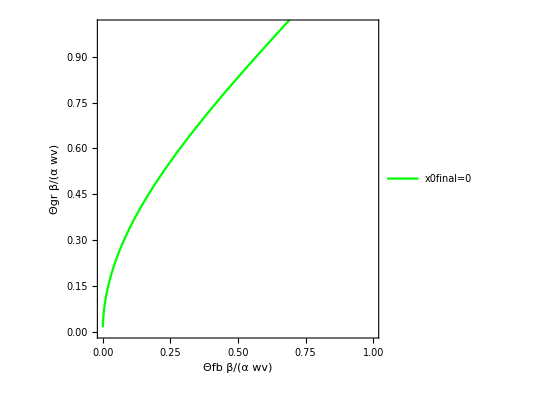

```mathematica
plotStyle[
Show[{
With[
{x0final=0},
ParametricPlot[
{
Θfb[λv,αv,wCompv,βv,Diffv,Lfinal,x0final]*(βv/(αv*wv)),
Θgr[λv,αv,wCompv,βv,Diffv,Lfinal,x0final]*(βv/(αv*wv))
},
{Lfinal,Lv, 10*λv},
PlotStyle->Green, 
PlotLegends->{"x0final=0"},
FrameLabel->{"Θfb β/(α wv)","Θgr β/(α wv)"},
	AspectRatio -> 1/1,
	AxesOrigin->{0, 0},
	PlotRange->{{0,1}, {0,1}}
]
](*,
ParametricPlot[
Table[
{
Θfb[λv,αv,wCompv,βv,Diffv,Lfinal,x0final],
Θgr[λv,αv,wCompv,βv, Diffv,Lfinal,x0final]
},
{x0final,0, wCompv,wCompv/10}],
{Lfinal,Lv,10*λv},
PlotStyle->Yellow
]*),
With[
{x0final=0.5*wCompv},
ParametricPlot[
{
{Θfb1*(βv/(αv*wv)),
Θgr1*(βv/(αv*wv))},
{Θfb2*(βv/(αv*wv)),
Θgr2*(βv/(αv*wv))}
},
{Lfinal,Lv, 10*λv},
PlotStyle->{Green, Orange}, 
FrameLabel->{"Θfb β/(α wv)","Θgr β/(α wv)"},
	AspectRatio -> 1/1,
	AxesOrigin->{0, 0}
]
](*,
ListPlot[{
{0.1*Θgrv*βv/(αv*wCompv), Θgrv*βv/(αv*wCompv)},
{Θfbv*βv/(αv*wCompv), Θgrv*βv/(αv*wCompv)}
},
PlotStyle->Red
]*)
}]]
```

```mathematica
Lv
```

1.8

```mathematica
wCompv
```

0.8

```mathematica
FindRoot[
 {Θgr[λv,  αv, wCompv, βv, Diffv, Lfinal, x0final] == Θgrv, Θfb[λv,  αv, wCompv, βv, Diffv, Lfinal, x0final] == Θfbv},
 {{Lfinal, Lv}, {x0final, wCompv/2}}
 ]
Lfinalv = Lfinal /. FindRoot[
    {Θgr[λv,  αv, wCompv, βv, Diffv, Lfinal, x0final] == Θgrv, Θfb[λv,  αv, wCompv, βv, Diffv, Lfinal, x0final] == Θfbv},
    {{Lfinal, Lv}, {x0final, wCompv/2}}
    ];
x0finalv = x0final /. FindRoot[
    {Θgr[λv,  αv, wCompv, βv, Diffv, Lfinal, x0final] == Θgrv, Θfb[λv,  αv, wCompv, βv, Diffv, Lfinal, x0final] == Θfbv},
    {{Lfinal, Lv}, {x0final, wCompv/2}}
    ];
```

{Lfinal→2.3899,x0final→0.401846}

```mathematica
FindRoot[
 Θfb[λv,  αv, wCompv, βv, Diffv, 0.9*Lfinalv, x0middle] == Θfbv,
 {x0middle, 0}
 ]
```

{x0middle→0.510131}

```mathematica
OnePlot[x0_,  L_]:=
plotStyle[ 
Show[{
Plot[
{
SolutionSteady[x,x0 (*x0*), λv (*λ*), αv, wCompv-x0(*w*), βv, Diffv, L],
SolutionSteady[x,L-wCompv(*x0*), λv (*λ*), αv, wCompv-x0(*w*), βv, Diffv(*D-scaling*), L],
Θgrv,
Θfbv
}, 
{x, 0, L},
PlotStyle->{colorsDict["Red"], colorsDict["Blue"],  {colorsDict["Gray"], Dashed},  {Orange, Dashed}},
	AspectRatio -> 1/1,
	AxesOrigin->{0, 0},
	FrameLabel->None,
	(*FrameTicks->None,*)
	PlotRange->{{0, Lfinalv},{0,0.7}}
],
Plot[
Θfbv*αv*χ[x, x0, wCompv-x0],
{x,0,  L}, 
Filling -> Bottom, 
FillingStyle ->colorsDict["Red"],
PlotStyle -> None
],
Plot[
Θfbv*αv*χ[x,L-wCompv, wCompv-x0],
{x,0,  L}, 
Filling -> Bottom, 
FillingStyle ->colorsDict["Blue"], 
PlotStyle -> None
]
}]];
```

```mathematica
Lfinalv
```

2.3899

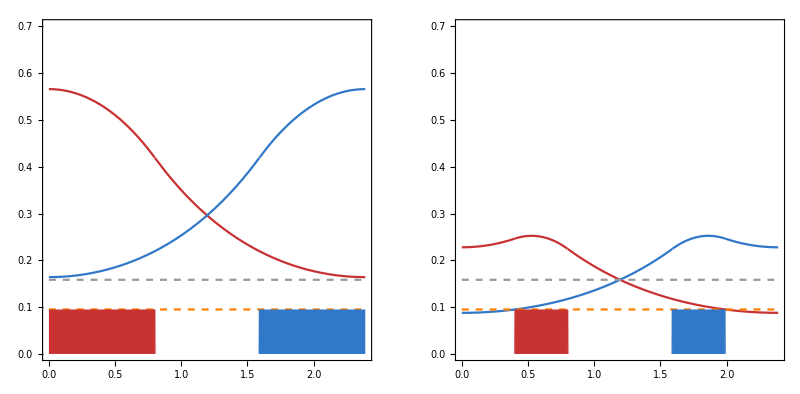

```mathematica
GraphicsRow[
{OnePlot[0,  Lfinalv],OnePlot[x0finalv,  Lfinalv]}
]
```